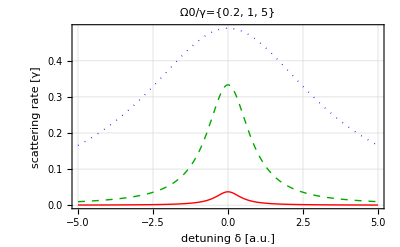

```mathematica
CommonPlotOpts={PlotStyle->{{Red,Dashing[∞]},{Darker[Green],Dashed},{Blue,Dotted}}};
CommonPlotOptsDisplay={Frame->True,GridLines->Automatic,LabelStyle->{FontFamily->"Helvetica",FontSize->2*10},ImageSize->2*{72 1/2.541*(8.6)}};
CommonPlotOptsPrint={Frame->True,GridLines->Automatic,LabelStyle->{FontFamily->"Helvetica",FontSize->8},ImageSize->{72 1/2.541*(8.6)}};
c=3*10^8;
h=6.626*10^-34;
hbar=h/(2*π);
kL=2*π/(852*10^-9);
S0=2*Ω0^2/γ^2;
paras={γ->1,Ω0->{0.2,1,5}};
(* set hbar * kL = 1  *)
Fcool[δ_]=γ/2*S0/(1+S0+4*δ^2/γ^2);
pl=Plot[Evaluate[Fcool [δ]/.paras],{δ,-5,5},PlotRange->{0,Full},FrameLabel->{"detuning δ [a.u.]","scattering rate [γ]"},PlotLabel->"Ω0/γ="<>ToString[Ω0/.paras],Evaluate@CommonPlotOpts,Evaluate@CommonPlotOptsDisplay,PlotRange->{0,1}]
```

```mathematica
plPrint=Show[pl,Evaluate@CommonPlotOptsPrint];
Export[NotebookDirectory[]<>FileBaseName[NotebookFileName[]]<>"_Plot.pdf",plPrint,"PDF"]
```

D:\ATI\Lehre\!meine Lehre\Quantenoptik 2_SoSe_16\Lecture 04 - Cooling and Trapping\LaserCooling01_Plot.pdf

```mathematica
Fmolasse[v_,δ_,η_]=η/2*S0/(1+S0+(2*(δ-η*kL*v)/γ)^2);
```

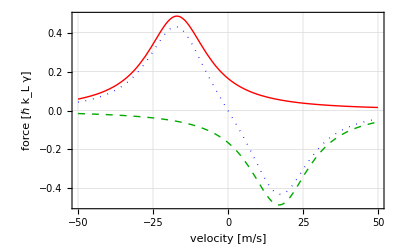

```mathematica
parasMol={γ->2*π*5*10^6,Ω0->2*π*20*10^6,δ->-2*π*20*10^6};
plMol=Plot[{Evaluate[Fmolasse [v,δ,1]/.parasMol],Evaluate[Fmolasse [v,δ,-1]/.parasMol],Evaluate[Fmolasse [v,δ,1]/.parasMol]+Evaluate[Fmolasse [v,δ,-1]/.parasMol]},{v,-50,50},PlotRange->All,FrameLabel->{"velocity [m/s]","force [ℏ k_L γ]"},Evaluate@CommonPlotOpts,Evaluate@CommonPlotOptsDisplay]
```

```mathematica
plMolPrint=Show[plMol,Evaluate@CommonPlotOptsPrint];
Export[NotebookDirectory[]<>FileBaseName[NotebookFileName[]]<>"_Plot_Molasse.pdf",plMolPrint,"PDF"]
```

D:\ATI\Lehre\!meine Lehre\Quantenoptik 2_SoSe_16\Lecture 04 - Cooling and Trapping\LaserCooling01_Plot_Molasse.pdf

```mathematica
ClearAll[S0];
```

```mathematica
(* friction coefficient for small v *)
Series[1/2*S0/(1+S0+(2*(δ-1*kL*v)/γ)^2)+-1/2*S0/(1+S0+(2*(δ+1*kL*v)/γ)^2),{v,0,1}]
```

(8 kL S0 δ v)/(γ^2 (1+S0+(4 δ^2)/γ^2)^2)+O[v]^2